## Lorentz Attractor

```mathematica
Remove["Global`*"]
```

```mathematica
rho := 25; T:=10.4898;
```

```mathematica
solution = NDSolve[{x'[t]==10*(y[t]-x[t]), y'[t]==x[t](rho-z[t])-y[t], z'[t]==x[t]y[t]-(8/3)*z[t], x[0]==10, y[0]==10, z[0]==10},{x,y,z},{t,0,0.01,T}];
```

```mathematica
Evaluate[{x[t],y[t],z[t]}/.solution];
```

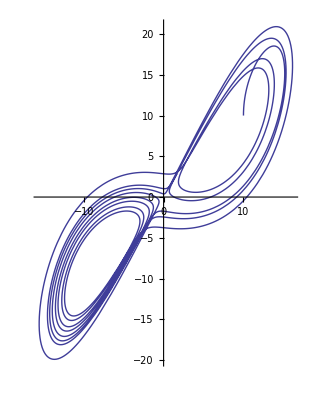

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.solution],{t,0,T}]
```

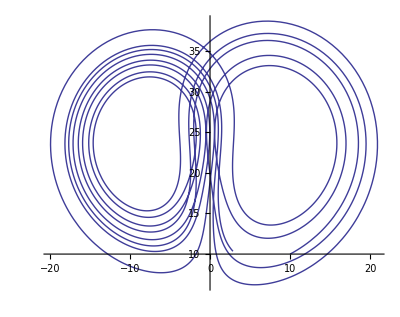

```mathematica
ParametricPlot[Evaluate[{y[t],z[t]}/.solution],{t,0,T}]
```

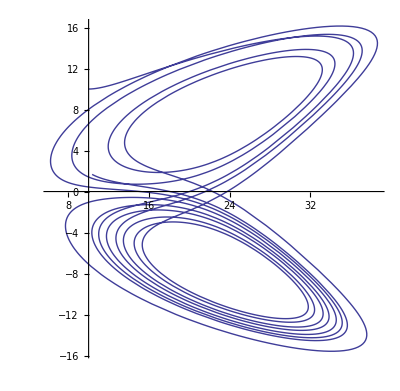

```mathematica
ParametricPlot[Evaluate[{z[t],x[t]}/.solution],{t,0,T}]
```

```mathematica
ParametricPlot3D[Evaluate[{z[t],x[t],y[t]}/.solution],{t,0,T}]
```

-Graphics3D-

## Wave Equation

```mathematica
Remove["Global`*"]
```

```mathematica
eqn1 = D[f[t,x],t,t] == D[f[t,x],x,x]
DSolve[eqn1,f,{t,x}]
```

f^(2,0)[t,x]==f^(0,2)[t,x]

{{f→Function[{t,x},C[1][-t+x]+C[2][t+x]]}}

## Diffusion Equation

```mathematica
Remove["Global`*"]
```

```mathematica
κ := 1
```

```mathematica
eqn2 = D[f[t,x],t] == (1/κ)*D[f[t,x],x,x]
DSolve[eqn2, f, {t,x}]
```

f^(1,0)[t,x]==f^(0,2)[t,x]

DSolve[f^(1,0)[t,x]==f^(0,2)[t,x],f,{t,x}]

```mathematica
sol := NDSolve[{eqn2, f[0,x]==Exp[-10*(x-0.5)^2]*Sin[Pi*x], f[t,0]==0, f[t,1]==0},{f[t,x]},{t,0,5},{x,0,1}]
```

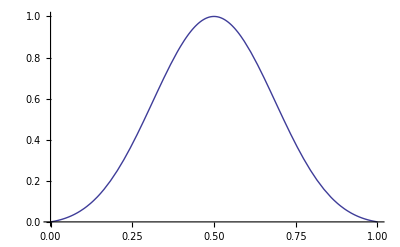

```mathematica
Plot[Evaluate[Abs[f[t,x]/.sol]/.t->0],{x,0,1},PlotRange->All]
```

```mathematica
Animate[Plot[Evaluate[Abs[f[t,x]/.sol]/.t->s],{x,0,1},PlotRange->All],{s,0,5},AnimationRunning->False]
```

```mathematica
soln := NDSolve[{eqn2, f[0,x]==0, f[t,0]==10, f[t,1]==10},{f[t,x]},{t,0,5},{x,0,1}]
```

```mathematica
Animate[Plot[Evaluate[Abs[f[t,x]/.soln]/.t->s],{x,0,1},PlotRange->All],{s,0,5},AnimationRunning->False]
```

## Wave Equation

```mathematica
Remove["Global`*"]
```

```mathematica
DSolve[D[u[t,x],t,t]==D[u[t,x],x,x],{u},{t,x}]
```

{{u→Function[{t,x},C[1][-t+x]+C[2][t+x]]}}

```mathematica
DirichletBCs[f_,x_,xm_]:=f-((((f/.x->-xm)-(f/.x->xm))/2)(Cos[(x+xm)*Pi/(2*xm)]+1)+(f/.x->xm))
```

```mathematica
DirichletBCs[Exp[-x^2],x,xm]/.x->xm
DirichletBCs[Exp[-x^2],x,xm]/.x->-xm
```

0

0

```mathematica
xm:=15
T:=50
(*try for two values of T -> 10, 50*)
(*one before and after the boundary is hit by the wave*)
```

```mathematica
sol := NDSolve[{D[u[t,x],t,t]==D[u[t,x],x,x],u[0,x]==DirichletBCs[Exp[-x^2],x,xm],u[t,-xm]==0,u[t,xm]==0,(D[u[t,x],t]/.t->0)==0},{u},{t,0,T},{x,-xm,xm}]
```

```mathematica
Plot3D[Evaluate[u[t,x]/.sol],{t,0,T},{x,-xm,xm},PlotRange->All]
```

-Graphics3D-

```mathematica
Animate[Plot[Evaluate[u[t,x]/.sol],{x,-xm,xm},PlotRange->All],{t,0,T},AnimationRunning->False]
```

## Schrodinger’s Equation

```mathematica
Remove["Global`*"]
```

```mathematica
DirichletBCs[f_,x_,xm_]:=f-((((f/.x->-xm)-(f/.x->xm))/2)(Cos[(x+xm)*Pi/(2*xm)]+1)+(f/.x->xm))
```

```mathematica
DirichletBCs[Exp[-x^2],x,xm]/.x->xm
DirichletBCs[Exp[-x^2],x,xm]/.x->-xm
```

0

0

```mathematica
SchrodingerEq = I*D[ψ[t,x],t]==-(1/2)*D[ψ[t,x],x,x]+6*Exp[-x^2]*ψ[t,x]
```

ⅈ ψ^(1,0)[t,x]==6 ⅇ^(-x^2) ψ[t,x]-1/2 ψ^(0,2)[t,x]

```mathematica
xm:=15
T:=5
```

```mathematica
DSolve[SchrodingerEq,{ψ},{t,x}]
```

DSolve[ⅈ ψ^(1,0)[t,x]==6 ⅇ^(-x^2) ψ[t,x]-1/2 ψ^(0,2)[t,x],{ψ},{t,x}]

```mathematica
sol := NDSolve[{SchrodingerEq, ψ[0,x]==DirichletBCs[Exp[-(x+3)^2],x,xm]*Exp[2*I*x],ψ[t,-xm]==0,ψ[t,xm]==0 },{ψ[t,x]},{t,0,T},{x,-xm,xm},AccuracyGoal->3,PrecisionGoal->3]
```

```mathematica
(*ByteCount[sol]/.10^6*) -> will tell me how much space is being taken up
```

```mathematica
Plot3D[Evaluate[Abs[ψ[t,x]]/.sol],{t,0,T},{x,-xm,xm},PlotRange->All]
```

-Graphics3D-

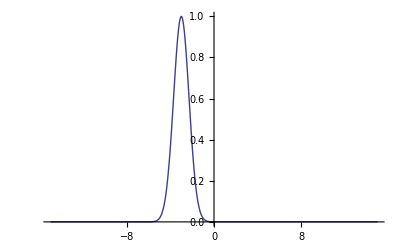

```mathematica
Plot[Evaluate[Abs[ψ[t,x]/.sol]/.t->0],{x,-xm,xm},PlotRange->All]
```

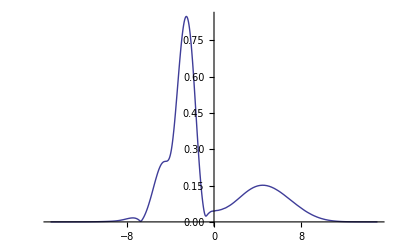

```mathematica
Plot[Evaluate[Abs[ψ[t,x]/.sol]/.t->2.5],{x,-xm,xm},PlotRange->All]
```

```mathematica
Manipulate[Plot[Evaluate[Abs[ψ[t,x]/.sol]/.t->s],{x,-xm,xm},PlotRange->All],{s,0,T}]
```

Plot::plln: Limiting value -xm in {x, -xm, xm} is not a machine-sized real number.